```mathematica
Clear["Global`*"]
```

## main

```mathematica
thisfolder=NotebookDirectory[];
rootfolder=StringSplit[thisfolder,"/"][[1;;Length[StringSplit[thisfolder,"/"]]-1]];
rootfolder=StringJoin[StringJoin[Flatten[Table[{"/",rootfolder[[j]]},{j,1,Length[rootfolder]}]]],"/"];
model=Import[StringJoin[thisfolder,"main_output.jam"],"Table"];
data=Import[StringJoin[thisfolder,"seriesP.jam"],"Table"];
model=Table[{model[[i,1]],model[[i,2]],model[[i,3]],data[[i,4]],model[[i,4]]},{i,1,Length[model]}];
epochs=Union[model[[All,4]]];
OOTs=Table[Max[Select[model,#[[4]]==epochs[[i]]&][[All,5]]],{i,1,Length[epochs]}];
j=0;Label[jloop];j=j+1;Subscript[mini, j]=Select[model,#[[4]]==epochs[[j]]&];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
temp=Flatten[Import[StringJoin[NotebookDirectory[],"bestmode.jam"],"Table"]];
Pdays=temp[[4]]
τ0=temp[[5]]
Msptrue=temp[[13]]
strue=temp[[14]] temp[[1]]
T14=temp[[15]];
T23=temp[[16]];West=(T14+T23)/2
```

59.9896

0

0.00314645

0.00915768

0.255778

```mathematica
xwidth=Max[Table[Max[Subscript[mini, j][[All,1]]]-Min[Subscript[mini, j][[All,1]]],{j,1,Length[epochs]}]];
yrange={Min[Table[Min[Subscript[mini, j][[All,5]]],{j,1,Length[epochs]}]],1};
yrange={yrange[[1]]-0.05(yrange[[2]]-yrange[[1]]),yrange[[2]]+0.05(yrange[[2]]-yrange[[1]])};
yrange={1-2strue^2,1};
yrange={yrange[[1]]-0.05(yrange[[2]]-yrange[[1]]),yrange[[2]]+0.05(yrange[[2]]-yrange[[1]])};
tmids=Table[Pdays Round[(Median[Subscript[mini, j][[All,1]]]-τ0)/Pdays]+τ0,{j,1,Length[epochs]}]
```

{0.,59.9896,119.979,179.969,239.959,299.948,359.938,419.927,479.917,539.907,599.896,659.886,719.876,779.865,839.855,899.845,959.834,1019.82,1079.81,1139.8,1199.79,1259.78,1319.77,1379.76}

## main

```mathematica
thisfolder=NotebookDirectory[];Clear[Msp];
rootfolder=StringSplit[thisfolder,"/"][[1;;Length[StringSplit[thisfolder,"/"]]-1]];
rootfolder=StringJoin[StringJoin[Flatten[Table[{"/",rootfolder[[j]]},{j,1,Length[rootfolder]}]]],"/"];
model=Import[StringJoin[thisfolder,"ghost_output.jam"],"Table"];
data=Import[StringJoin[thisfolder,"seriesP.jam"],"Table"];
model=Table[{model[[i,1]],model[[i,2]],model[[i,3]],data[[i,4]],model[[i,4]]},{i,1,Length[model]}];
epochs=Union[model[[All,4]]];
OOTs=Table[Max[Select[model,#[[4]]==epochs[[i]]&][[All,5]]],{i,1,Length[epochs]}];
j=0;Label[jloop];j=j+1;Subscript[gini, j]=Select[model,#[[4]]==epochs[[j]]&];Subscript[tmiddy, j]=Sum[Subscript[gini, j][[i,1]](Subscript[gini, j][[i,5]]-1),{i,1,Length[Subscript[gini, j]]}]/Sum[(Subscript[gini, j][[i,5]]-1),{i,1,Length[Subscript[gini, j]]}];Subscript[ttv, j]=Subscript[tmiddy, j]-Pdays Round[(Median[Subscript[gini, j][[All,1]]]-τ0)/Pdays]-τ0;Subscript[ttvmoon, j]=Subscript[tmiddy, j]-(1/Msp)Subscript[ttv, j];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
outofplantimes=Select[Flatten[Table[Table[Subscript[gini, j][[i,{1,5}]],{i,1,Length[Subscript[gini, j]]}],{j,1,Length[epochs]}],1],!(#[[2]]<1)&][[All,1]];
Length[outofplantimes]
temp2=Flatten[Table[Table[{Subscript[mini, j][[i,1]],Subscript[mini, j][[i,5]]-Subscript[gini, j][[i,5]]},{i,1,Length[Subscript[mini, j]]}],{j,1,Length[epochs]}],1];
Length[temp2]
temp2=Select[temp2,MemberQ[outofplantimes,#[[1]]]&];
Length[temp2]
Δχ2theoretical=Sum[(temp2[[i,2]]/Δ)^2,{i,1,Length[temp2]}]
ttvtab=Table[{j,Subscript[tmiddy, j],Subscript[ttv, j]},{j,1,Length[epochs]}];
Export[StringJoin[NotebookDirectory[],"ttv.dat"],ttvtab,"Table"]
```

60262

70488

60262

0.+0.0000594867/Δ^2

/Users/davidkipping/Storage1/Work/Documents/Transit_Work/PAPERS/MoonFold/simulate/Jup-Super/f1.0/ttv.dat

### attempt a moon fold

```mathematica
Mspgrid=Table[10^x,{x,-3,0,0.01}];
k=0;Label[kloop];k=k+1;j=0;Label[jloop];j=j+1;Subscript[outplan, j]=Select[Subscript[mini, j][[All,{1,5}]],!(Subscript[tmiddy, j]-0.51T14<#[[1]]<Subscript[tmiddy, j]+0.51T14)&];Subscript[inmoon, j]=Select[Subscript[outplan, j],((Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]])-0.5West<#[[1]]<(Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]])+0.5West)&];Subscript[outmoon, j]=Select[Subscript[outplan, j],!((Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]])-0.5West<#[[1]]<(Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]])+0.5West)&];If[j<Length[epochs],Goto[jloop]];inmoonall=Flatten[Table[Subscript[inmoon, j],{j,1,Length[epochs]}],1];outmoonall=Flatten[Table[Subscript[outmoon, j],{j,1,Length[epochs]}],1];outplanall=Flatten[Table[Subscript[outplan, j],{j,1,Length[epochs]}],1];μinmoon=Mean[inmoonall[[All,2]]];μoutmoon=Mean[outmoonall[[All,2]]];μoutplan=Mean[outplanall[[All,2]]];Subscript[δ, k]=μoutmoon-μinmoon;χ2null=Sum[((inmoonall[[i,2]]-μoutplan)/Δ)^2,{i,1,Length[inmoonall]}]+Sum[((outmoonall[[i,2]]-μoutplan)/Δ)^2,{i,1,Length[outmoonall]}];χ2moon=Sum[((inmoonall[[i,2]]-μinmoon)/Δ)^2,{i,1,Length[inmoonall]}]+Sum[((outmoonall[[i,2]]-μoutmoon)/Δ)^2,{i,1,Length[outmoonall]}];Subscript[Δχ2, k]=(χ2null-χ2moon);If[k<Length[Mspgrid],Goto[kloop]];
result=Table[{Mspgrid[[k]],Subscript[δ, k],Subscript[Δχ2, k],Simplify[Subscript[Δχ2, k]/Δχ2theoretical]},{k,1,Length[Mspgrid]}];
```

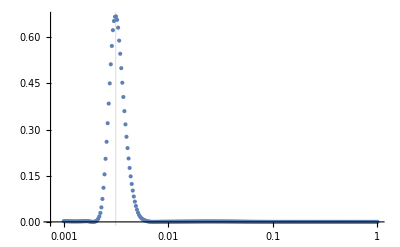

```mathematica
ListLogLinearPlot[result[[All,{1,4}]],GridLines->{{Msptrue},{}},PlotRange->{All,{All,All}}]
```

```mathematica
temp=result;
temp=Table[{temp[[i,1]],temp[[i,2]],temp[[i,2]]/strue^2,temp[[i,3]]/.Δ->10^(-3),temp[[i,4]]},{i,1,Length[temp]}];
temp=Select[temp,NumberQ[#[[2]]]&];
Export[StringJoin[NotebookDirectory[],"Msp_grid.dat"],temp,"Table"]
```

/Users/davidkipping/Storage1/Work/Documents/Transit_Work/PAPERS/MoonFold/simulate/Jup-Super/f1.0/Msp_grid.dat

```mathematica
Mspbestfit=Select[result,#[[4]]==Max[result[[All,4]]]&][[1,1]];
height=Select[result,#[[4]]==Max[result[[All,4]]]&][[1,4]];
temp=Select[result,#[[1]]<Mspbestfit&&#[[4]]<0.5height&];
Mspbestfitlow=Select[temp,#[[4]]==Max[temp[[All,4]]]&][[1,1]];
temp=Select[result,#[[1]]>Mspbestfit&&#[[4]]<0.5height&];
Mspbestfithigh=Select[temp,#[[4]]==Max[temp[[All,4]]]&][[1,1]];
Print["Msp = ",Mspbestfit," +/- ",(Mspbestfithigh-Mspbestfitlow)/2]
Abs[(Mspbestfit-Msptrue)/((Mspbestfithigh-Mspbestfitlow)/2)]
```

Msp = 0.00316228 +/- 0.000630092

0.0251206

### best fold

```mathematica
Mspbestfit=Msptrue
```

0.00314645

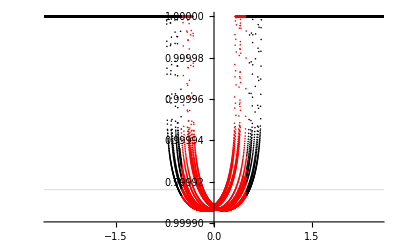

```mathematica
j=0;Label[jloop];j=j+1;Subscript[inmoon, j]=Select[Subscript[mini, j][[All,{1,5}]],((Subscript[ttvmoon, j]/.Msp->Mspbestfit)-0.5West<#[[1]]<(Subscript[ttvmoon, j]/.Msp->Mspbestfit)+0.5West)&&!(Subscript[tmiddy, j]-0.51T14<#[[1]]<Subscript[tmiddy, j]+0.51T14)&];Subscript[inmoon, j]=Table[{(Subscript[inmoon, j][[i,1]]-(Subscript[ttvmoon, j]/.Msp->Mspbestfit))/West,Subscript[inmoon, j][[i,2]]},{i,1,Length[Subscript[inmoon, j]]}];Subscript[outmoon, j]=Select[Subscript[mini, j][[All,{1,5}]],!((Subscript[ttvmoon, j]/.Msp->Mspbestfit)-0.5West<#[[1]]<(Subscript[ttvmoon, j]/.Msp->Mspbestfit)+0.5West)&&!(Subscript[tmiddy, j]-0.51T14<#[[1]]<Subscript[tmiddy, j]+0.51T14)&];Subscript[outmoon, j]=Table[{(Subscript[outmoon, j][[i,1]]-(Subscript[ttvmoon, j]/.Msp->Mspbestfit))/West,Subscript[outmoon, j][[i,2]]},{i,1,Length[Subscript[outmoon, j]]}];Subscript[outplan, j]=Select[Subscript[mini, j][[All,{1,5}]],!(Subscript[tmiddy, j]-0.51T14<#[[1]]<Subscript[tmiddy, j]+0.51T14)&];If[j<Length[epochs],Goto[jloop]];inmoonall=Flatten[Table[Subscript[inmoon, j],{j,1,Length[epochs]}],1];outmoonall=Flatten[Table[Subscript[outmoon, j],{j,1,Length[epochs]}],1];outplanall=Flatten[Table[Subscript[outplan, j],{j,1,Length[epochs]}],1];
μinmoon=Mean[inmoonall[[All,2]]];μoutmoon=Mean[outmoonall[[All,2]]];μoutplan=Mean[outplanall[[All,2]]];δbest=μoutmoon-μinmoon;χ2null=Sum[((inmoonall[[i,2]]-μoutplan)/Δ)^2,{i,1,Length[inmoonall]}]+Sum[((outmoonall[[i,2]]-μoutplan)/Δ)^2,{i,1,Length[outmoonall]}];χ2moon=Sum[((inmoonall[[i,2]]-μinmoon)/Δ)^2,{i,1,Length[inmoonall]}]+Sum[((outmoonall[[i,2]]-μoutmoon)/Δ)^2,{i,1,Length[outmoonall]}];Δχ2best=(χ2null-χ2moon);
ListPlot[{inmoonall,outmoonall},PlotStyle->{Red,Black},PlotRange->{{-2.5,2.5},All},GridLines->{{},{1-strue^2}}]
```

```mathematica
Δ0=1000*10^(-6);
√(Δχ2best/.Δ->Δ0)
√(Δχ2theoretical/.Δ->Δ0)
```

6.30494

7.71276

```mathematica
inmoonallnoise=Sort[Table[{inmoonall[[i,1]],10^6(RandomReal[NormalDistribution[inmoonall[[i,2]],Δ0]]-1)},{i,1,Length[inmoonall]}]];
outmoonallnoise=Sort[Table[{outmoonall[[i,1]],10^6(RandomReal[NormalDistribution[outmoonall[[i,2]],Δ0]]-1)},{i,1,Length[outmoonall]}]];
tbin=0.1;
ttmin=Floor[Min[outmoonallnoise[[All,1]]],tbin];
ttmax=Ceiling[Max[outmoonallnoise[[All,1]]],tbin];
datain=Sort[Join[inmoonallnoise,outmoonallnoise]];
j=0;Label[jloop];j=j+1;tab=Select[datain,ttmin+(j-1)tbin<#[[1]]<ttmin+j tbin&];Subscript[α, j]={ttmin+(j-0.5)tbin,Mean[tab[[All,2]]],StandardDeviation[tab[[All,2]]]/(√(Length[tab]-1))};If[ttmin+j tbin<ttmax,Goto[jloop]];
binned=Table[Subscript[α, jj],{jj,1,j}];
binned=Select[binned,NumberQ[#[[2]]]&&NumberQ[#[[3]]]&];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

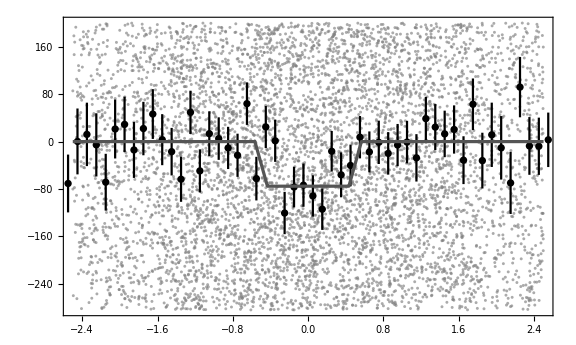

```mathematica
<<ErrorBarPlots`
fn[δ_,t14_,t23_,t_]:=Piecewise[{{0,Abs[t]>0.5t14},{-δ,Abs[t]<0.5t23},{(2 (1+ δ))/(t14- t23)t-((t23+ t14 δ)/(t14-t23)),0.5t23<t<0.5t14},{-(2 (1+ δ))/(t14- t23)t-((t23+ t14 δ)/(t14-t23)),-0.5t14<t<-0.5t23}}];
xrange2={-2.5,2.5};
yrange2={10^6(-0.2Δ0-1.0strue^2),0.2 10^6 Δ0};
test1=Select[inmoonallnoise,xrange2[[1]]<#[[1]]<xrange2[[2]]&&yrange2[[1]]<#[[2]]<yrange2[[2]]&];
test2=Select[outmoonallnoise,xrange2[[1]]<#[[1]]<xrange2[[2]]&&yrange2[[1]]<#[[2]]<yrange2[[2]]&];
truefold=Show[ListPlot[{test1,test2},PlotStyle->{Directive[Gray,Opacity[0.66]],Directive[Gray,Opacity[0.66]]},PlotRange->{xrange2,yrange2},Frame->True,ImageSize->Large,AspectRatio->0.6,Axes->None,BaseStyle->{FontFamily->"CMU Serif",FontSize->20}],ErrorListPlot[binned[[All,{1,2,3}]],PlotStyle->Black],Plot[fn[δbest*10^6,T14/West,T23/West,t],{t,-2.5,2.5},Exclusions->None,PlotStyle->Directive[Lighter[Black],Thickness[0.004]]]]
Export[StringJoin[thisfolder,"fold.pdf"],truefold];
```

```mathematica
tbin=0.1(T14+T23)/2;j=0;Label[jloop];j=j+1;Subscript[nini, j]=Table[{Subscript[mini, j][[i,1]],10^6(RandomReal[NormalDistribution[Subscript[mini, j][[i,5]],Δ0]]-1)},{i,1,Length[Subscript[mini, j]]}];Subscript[xini, j]=Table[{Subscript[mini, j][[i,1]],10^6(Subscript[mini, j][[i,5]]-1)},{i,1,Length[Subscript[mini, j]]}];ttmin=Min[Subscript[nini, j][[All,1]]];ttmax=Max[Subscript[nini, j][[All,1]]];k=0;Label[kloop];k=k+1;tab=Select[Subscript[nini, j],ttmin+(k-1)tbin<#[[1]]<ttmin+k tbin&];Subscript[β, k]={ttmin+(k-0.5)tbin,Mean[tab[[All,2]]],StandardDeviation[tab[[All,2]]]/√(Length[tab]-1)};If[ttmin+k tbin<ttmax,Goto[kloop]];Subscript[bini, j]=Table[Subscript[β, kk],{kk,1,k}];Subscript[nlotty, j]=Show[ListPlot[Subscript[nini, j],PlotRange->{{tmids[[j]]-0.5xwidth,tmids[[j]]+0.5xwidth},{10^6(-Δ0-1.2strue^2),10^6 Δ0}},Frame->True,ImageSize->Large,AspectRatio->0.6,Axes->None,GridLines->{{{Subscript[tmiddy, j],Directive[Lighter[Blue],Thickness[0.004]]},Pdays Round[(Median[Subscript[gini, j][[All,1]]]-τ0)/Pdays]+τ0,{Subscript[ttvmoon, j]/.Msp->Mspbestfit,Directive[Lighter[Red],Thickness[0.004]]}},{}},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotStyle->Directive[Gray,Opacity[0.66],Thickness[0.004]]],ErrorListPlot[Subscript[bini, j],PlotStyle->Black],ListPlot[Subscript[xini, j][[All,{1,2}]],Joined->True,PlotStyle->Directive[Lighter[Black],Thickness[0.004]],PlotRange->All]];Export[StringJoin[thisfolder,ToString[j],"_noised.pdf"],Subscript[nlotty, j]];If[j<Length[epochs],Goto[jloop]];
```

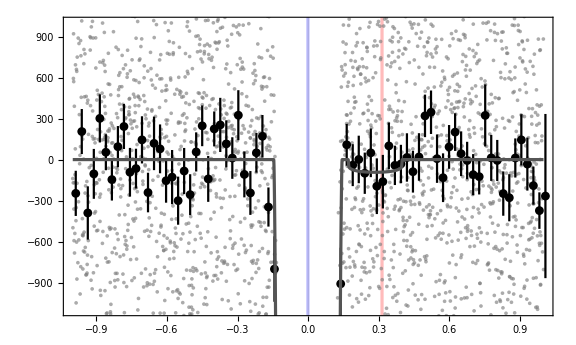

```mathematica
Subscript[nlotty, 1]
```

### global fold

```mathematica
test=Flatten[Table[Subscript[mini, j][[All,{1,5}]],{j,1,Length[epochs]}],1];
test=Sort[Table[{test[[i,1]]-Pdays Round[test[[i,1]]/Pdays],10^6(RandomReal[NormalDistribution[test[[i,2]],Δ0]]-1)},{i,1,Length[test]}]];
tttmin=Min[test[[All,1]]];tttmax=Max[test[[All,1]]];k=0;Label[kloop];k=k+1;tab=Select[test,tttmin+(k-1)tbin<#[[1]]<tttmin+k tbin&];Subscript[γ, k]={tttmin+(k-0.5)tbin,Mean[tab[[All,2]]],StandardDeviation[tab[[All,2]]]/√(Length[tab]-1)};If[tttmin+k tbin<tttmax,Goto[kloop]];best=Table[Subscript[γ, kk],{kk,1,k}];
```

```mathematica
gest=Flatten[Table[Subscript[gini, j][[All,{1,5}]],{j,1,Length[epochs]}],1];
gest=Sort[Table[{gest[[i,1]]-Pdays Round[gest[[i,1]]/Pdays],10^6(gest[[i,2]]-1)},{i,1,Length[gest]}]];
```

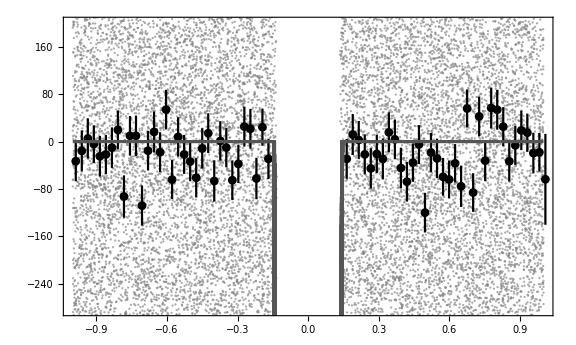

```mathematica
ex=Show[ListPlot[test,PlotRange->{{-1,1},yrange2},Frame->True,ImageSize->Large,AspectRatio->0.6,Axes->None,BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotStyle->Directive[Gray,Opacity[0.66],Thickness[0.004]]],ErrorListPlot[best,PlotStyle->Black],ListPlot[gest[[All,{1,2}]],Joined->True,PlotStyle->Directive[Lighter[Black],Thickness[0.004]],PlotRange->All]]
```

```mathematica
Export[StringJoin[thisfolder,"singlefold.pdf"],ex]
```

/Users/davidkipping/Storage1/Work/Documents/Transit_Work/PAPERS/MoonFold/simulate/Jup-Super/f1.0/singlefold.pdf